## Definition

```mathematica
(*Run this before others*)
(*------------------------*)
(*SimTrans:generate affine transformation based on matrix or scale and fixed point*)
SimTrans[s_,fp_]:=Module[{mat},
mat=If[MatrixQ[s],s,ScalingMatrix[Table[s,Length[fp]]]];
AffineTransform[{mat,fp-mat.fp}]];
(*ConvertFun:Unused*)
ConvertFun[f_]:=Module[{g},
g=f;
If[!ValueQ[f["ArgumentLength"]],
g["AffineQ"]=False;
g["Self"]=False;
Which[
ValueQ[f[{0,0}]],g["ArgumentLength"]=2,
ValueQ[f[{0}]],g["ArgumentLength"]=1,
ValueQ[f[{0,0,0}]],g["ArgumentLength"]=3
]];
If[!ValueQ[g["ArgumentLength"]],
g["ArgumentLength"]=-1];
g
];
CalcDim[f_]:=If[IntegerQ[f["ArgumentLength"]],
f["ArgumentLength"],
Which[(*calc dimension*)
NumberQ[f[{0,0}][[1]]],2,
NumberQ[f[{0}][[1]]],1,
NumberQ[f[{0,0,0}][[1]]],3
]
];
(*FixPoint:esitimate fixed point*)
FixPoint[f_]:=
If[BooleanQ[f["AffineQ"]],
Inverse[IdentityMatrix[f["ArgumentLength"]]-f["AffineMatrix"]].f["AffineVector"],
Nest[f,Table[1.0,CalcDim[f]],10]
];
Options[DrawFrac]={Method->Automatic,MaxIterations->Automatic,Axes->False,"Approximation"->True,"Size"->0.2};
(*DrawFracL:draw graphs*)
DrawFrac[f_,opts:OptionsPattern[]]:=(*sf:List of Transformation;t:iteration count,default to make 10000 points*)
Module[{sf,ls,l,c,ti,md,pr,ax,ap,sst,afq,line,sz},
ti=OptionValue[MaxIterations];
md=OptionValue[Method];
ax=OptionValue[Axes];
ap=OptionValue["Approximation"];
sz=OptionValue["Size"];
sf=f;
afq=AllTrue[sf,NumberQ[#["ArgumentLength"]]&];
If[!afq&&md=="Region",Message[DrawFrac::ch];Abort[]];
ls=CalcDim/@sf;
(*find if dimensions are same*)
If[!AllTrue[ls,SameQ[First[ls],#]&],Message[DrawFrac::wd,ls];Abort[]];
l=ls[[1]];(*dimension*)
c=Length[sf];
If[ti==Automatic,ti=If[l==1,Floor[Log[c,100]],Floor[Log[c,10000]]]];
(*choose method*)
If[md==Automatic,md=Switch[l,1,"Points",2,"Points",
3,If[afq,"Region","Points"]]];
If[!MemberQ[{"Points","Region","Lines"},md],Message[DrawFrac::md];Abort[]];
Switch[md,
"Points",
sz=sz/10;
If[ap,sst=N[Through[sf[#]]]&,sst=Through[sf[#]]&];
Switch[l,
1,
NumberLinePlot[Flatten[#],PlotStyle->{PointSize[Small],Opacity[1]},Axes->ax]&/@NestList[Flatten[Map[sst,#1],1]&,{{0}},ti](*//GraphicsColumn*),
2,
(*ListPlot[#,PlotStyle->{PointSize[Small],Opacity[1]},Axes->False,PlotRange->{{-1,1},{-1,1}},AspectRatio->1,ImagePadding->None]*)MapThread[Graphics[{PointSize[#1],Gray,Point[#2]},Axes->ax]&,{Table[sz*0.85^n,{n,0,ti}],NestList[Flatten[Map[sst,#1],1]&,{{0,0}},ti]}],
3,
MapThread[Graphics3D[{PointSize[#1],Gray,Point[#2]},Axes->ax]&,{Table[sz*0.85^n,{n,0,ti}],NestList[Flatten[Map[sst,#1],1]&,{{0,0,0}},ti]}],
_,Message[DrawFrac::wd,ls];Abort[]
],
"Lines",
sz=sz*3;
If[ap,
sst[lines_]:=Flatten[ReplaceAll[Line[pts_]:>Line[#/@pts]][lines]&/@sf],
sst[lines_]:=Flatten[ReplaceAll[Line[pts_]:>Line[#/@pts]][lines]&/@sf]
];
Switch[l,
1,
line=MeshPrimitives[ConvexHullMesh[FixPoint/@sf],1];
Graphics[{AbsoluteThickness[sz],#},Axes->ax,AspectRatio->1/5]&/@(NestList[sst,line,ti]/.Line[{{x_},{y_}}]:>Line[{{x,0},{y,0}}]),
2,
line=MeshPrimitives[ConvexHullMesh[FixPoint/@sf],1];
Graphics[{AbsoluteThickness[sz],#},Axes->ax]&/@NestList[sst,line,ti]
,
3,
line=MeshPrimitives[ConvexHullMesh[FixPoint/@sf],1];
Graphics3D[{AbsoluteThickness[sz],#},Axes->ax,Boxed->ax]&/@NestList[sst,line,ti],
_,Message[DrawFrac::wd,ls];Abort[]
],
"Region",
Switch[l,
1,
If[ap,
sst[lines_]:=Flatten[ReplaceAll[Line[pts_]:>Line[#/@pts]][lines]&/@sf],
sst[lines_]:=Flatten[ReplaceAll[Line[pts_]:>Line[#/@pts]][lines]&/@sf]
];
line=MeshPrimitives[ConvexHullMesh[FixPoint/@sf],1];
Graphics[{AbsoluteThickness[sz],#},Axes->ax,AspectRatio->1/5]&/@(NestList[sst,line,ti]/.Line[{{x_},{y_}}]:>Line[{{x,0},{y,0}}]),
2,
If[ap,sst=N[FixPoint[#]]&,sst=FixPoint];
Graphics[{EdgeForm[],#},Axes->ax]&/@NestList[RegionUnion[Through[sf[#]]]&,ConvexHullMesh[sst/@sf](*Cube[]*),ti],
3,
If[ap,sst=N[FixPoint[#]]&,sst=FixPoint];
Graphics3D[{EdgeForm[],#},Axes->ax,Boxed->ax]&/@NestList[RegionUnion[Through[sf[#]]]&,ConvexHullMesh[sst/@sf](*Cube[]*),ti],
_,Message[DrawFrac::wd,ls];Abort[]
]
]
]
DrawFrac::md="Method:Points,ConvexHull,Lines";
DrawFrac::ch="Method ConvexHull does not apply to non affine transformation";
DrawFrac::wd="Dimension `1` should be same and less than 3";
```

## Discription

### Transformation Function

AffineTransform generate transformation function based on a matrix and affine vector

```mathematica
AffineTransform[{{{Subscript[a, 1,1],Subscript[a, 1,2]},{Subscript[a, 2,1],Subscript[a, 2,2]}},{Subscript[b, 1],Subscript[b, 2]}}]
```

TransformationFunction[(a_(1,1) | a_(1,2) | b_1
a_(2,1) | a_(2,2) | b_2
0 | 0 | 1)]

There are identity, scaling, rotation matrix, etc.

```mathematica
IdentityMatrix[2]//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
ScalingMatrix[{1/3,1/2,-1/2}]//MatrixForm
```

(1/3 | 0 | 0
0 | 1/2 | 0
0 | 0 | -1/2)

```mathematica
RotationMatrix[Pi/3]//MatrixForm
```

(1/2 | -(√3)/2
(√3)/2 | 1/2)

```mathematica
EulerMatrix[{Pi/2,Pi/3,-Pi/6}]//MatrixForm
```

(1/2 | -(√3)/2 | 0
(√3)/4 | 1/4 | (√3)/2
-3/4 | -(√3)/4 | 1/2)

SimTrans is used to calculate TransformationFunction with known scale factor or matrix and fixed point, it allows two ways of input.

```mathematica
SimTrans[1/2,{0,0,1}](*scale factor*)
```

TransformationFunction[(1/2 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | 1/2 | 1/2
0 | 0 | 0 | 1)]

```mathematica
SimTrans[RotationMatrix[Pi/6].ScalingMatrix[{1/3,1/2}],{-1,1}](*matrix*)
```

TransformationFunction[(1/(2 √3) | -1/4 | 1/12 (-9+2 √3)
1/6 | (√3)/4 | 1/12 (14-3 √3)
0 | 0 | 1)]

TransformationFunction can express fractional linear transformation ，from r  to  (A.r+b)/(c.r+d).

```mathematica
LinearFractionalTransform[{{{1,2},{3,4}}, {5,6},{7,8}}]
```

TransformationFunction[(1 | 2 | 5
3 | 4 | 6
7 | 8 | 1)]

### Graphic

The main input is sequence of TransformationFunction

```mathematica
(*Cantor Set*)
can={AffineTransform[{ScalingMatrix[{1/3}],{0}}],
AffineTransform[{ScalingMatrix[{1/3}],{2/3}}]}
```

{TransformationFunction[(1/3 | 0
0 | 1)],TransformationFunction[(1/3 | 2/3
0 | 1)]}

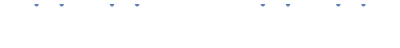
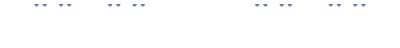
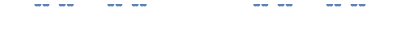
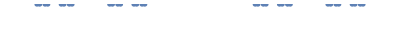
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
pt=DrawFrac[can]
```

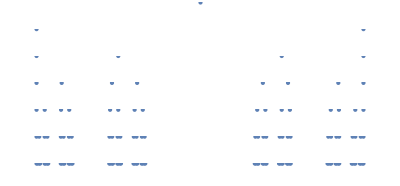

```mathematica
pt//GraphicsColumn
```

The Method option controls the drawing method, with selectable methods including “Points”, “Lines”, and “Region”, representing drawing points, lines, or convex hull regions. The default method is to draw points in one and two dimensions, and use convex hull regions in three dimensions. Drawing regions with custom functions is more difficult and currently does not support using the convex hull method for custom functions.

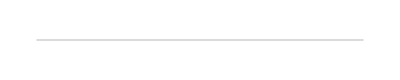
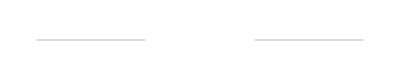
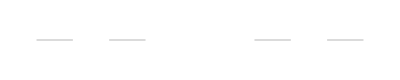
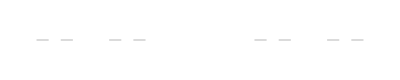
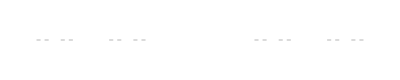
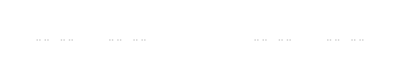
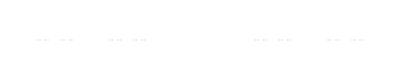

```mathematica
DrawFrac[can,Method->"Region"]
```

```mathematica
(*Sierpinski Triangle*)
strig={AffineTransform[{ScalingMatrix[{1/2,1/2}],{0,1/2}}],AffineTransform[{ScalingMatrix[{1/2,1/2}],{Sqrt[3]/6,0}}],AffineTransform[{ScalingMatrix[{1/2,1/2}],{-Sqrt[3]/6,0}}]}
```

{TransformationFunction[(1/2 | 0 | 0
0 | 1/2 | 1/2
0 | 0 | 1)],TransformationFunction[(1/2 | 0 | 1/(2 √3)
0 | 1/2 | 0
0 | 0 | 1)],TransformationFunction[(1/2 | 0 | -1/(2 √3)
0 | 1/2 | 0
0 | 0 | 1)]}

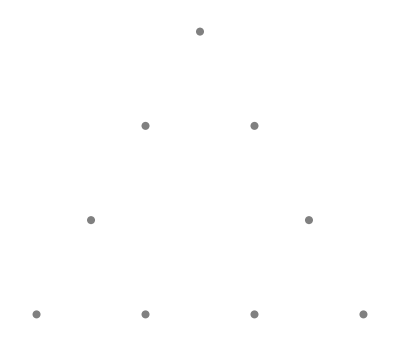
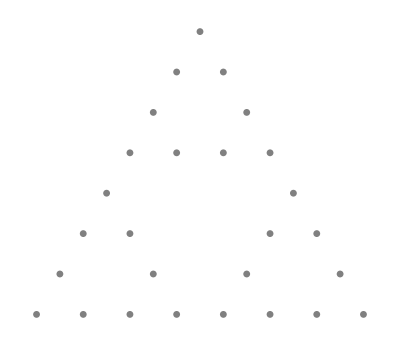
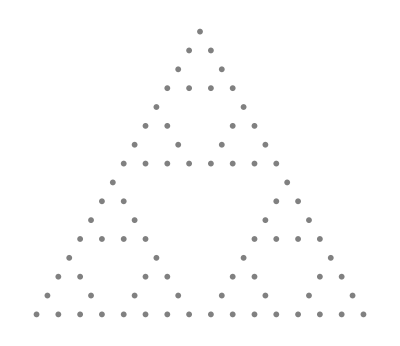
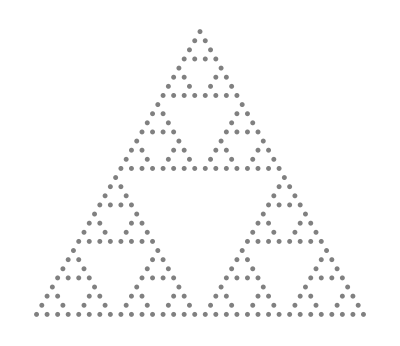
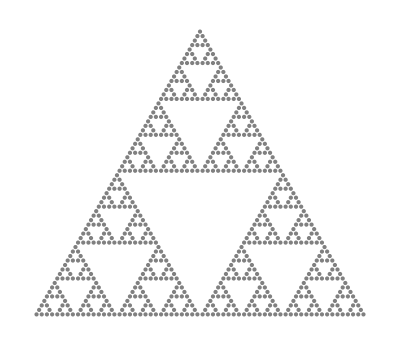
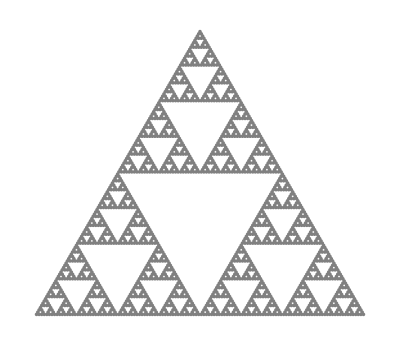
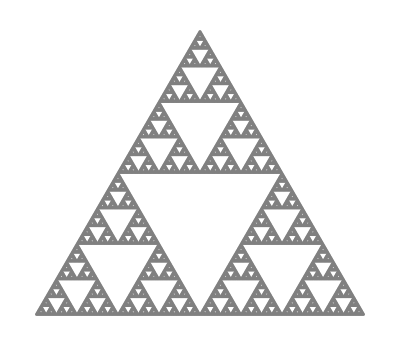
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawFrac[strig]
```

If you want to use functions other than linear transformations, use the following format: f[{x_, y_}] := {f_1(x, y), f_2(x, y)}. This format will be processed within the plotting function to match the appropriate method.

```mathematica
ff[{x_,y_}]:={x/2+Sin[x]/10,y/2+1/2};
mstrig={ff,AffineTransform[{ScalingMatrix[{1/2,1/2}],{Sqrt[3]/6,0}}],AffineTransform[{ScalingMatrix[{1/2,1/2}],{-Sqrt[3]/6,0}}]}
```

{ff,TransformationFunction[(1/2 | 0 | 1/(2 √3)
0 | 1/2 | 0
0 | 0 | 1)],TransformationFunction[(1/2 | 0 | -1/(2 √3)
0 | 1/2 | 0
0 | 0 | 1)]}

```mathematica
CalcDim/@mstrig
```

{2,2,2}

Use the MaxIterations option to control the number of iterations, with the default being 10,000 points.

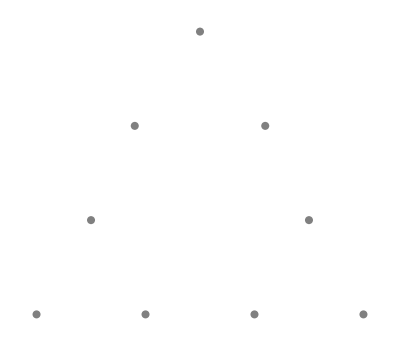
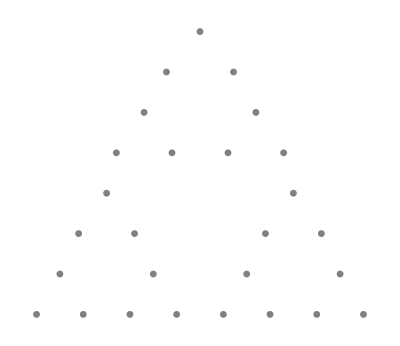
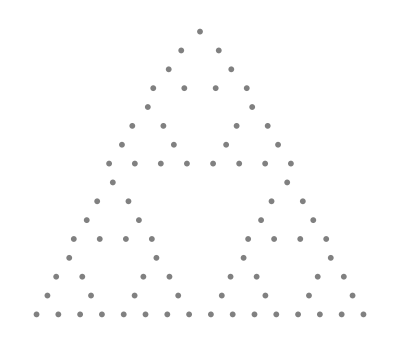
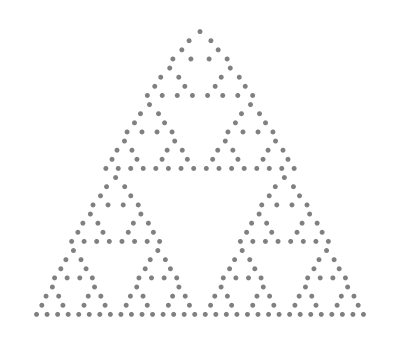
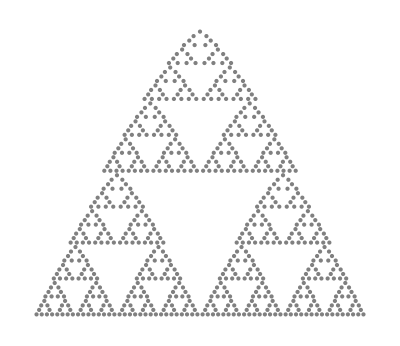
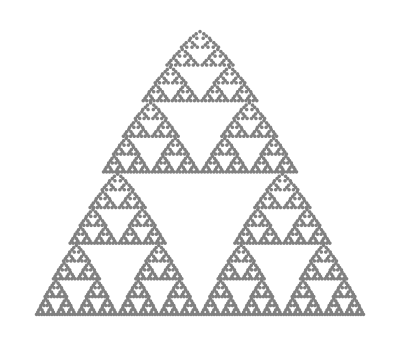
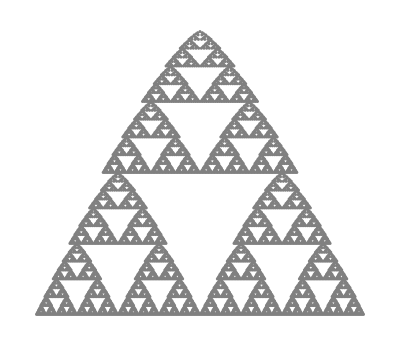
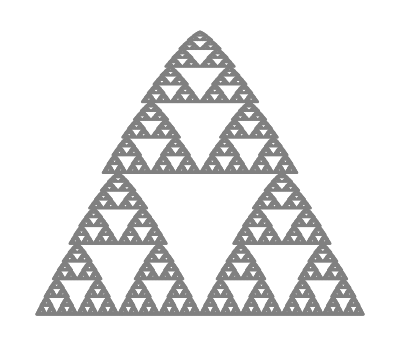
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawFrac[mstrig,Method->"Points",MaxIterations->9]
```

Other examples

```mathematica
vcurve={AffineTransform[{ScalingMatrix[{1/3,1/3}],{0,0}}],AffineTransform[{RotationMatrix[Pi/3].ScalingMatrix[{1/3,1/3}],{1/3,0}}],AffineTransform[{RotationMatrix[-Pi/3].ScalingMatrix[{1/3,1/3}],{1/2,Sqrt[3]/6}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{2/3,0}}]};
```

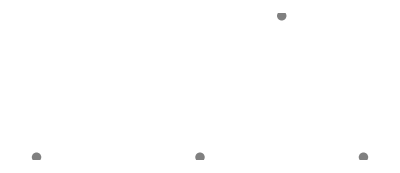
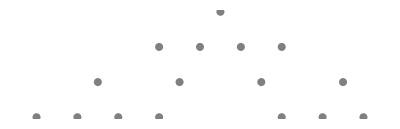
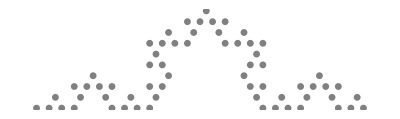
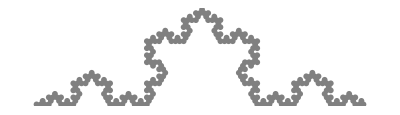
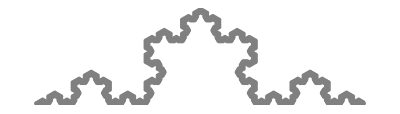
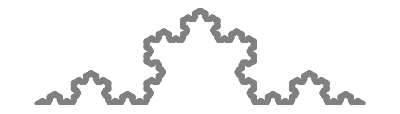
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawFrac[vcurve]
```

```mathematica
scarpet={AffineTransform[{ScalingMatrix[{1/3,1/3}],{0,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{0,1/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{0,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{1/3,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{1/3,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{2/3,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{2/3,1/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3}],{2/3,2/3}}]};
```


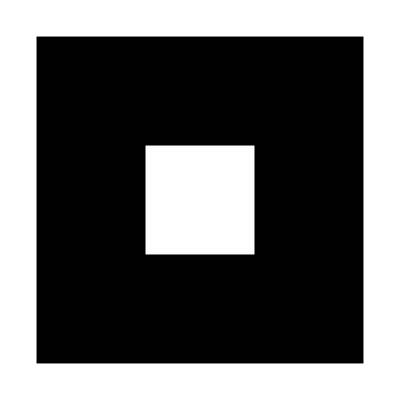
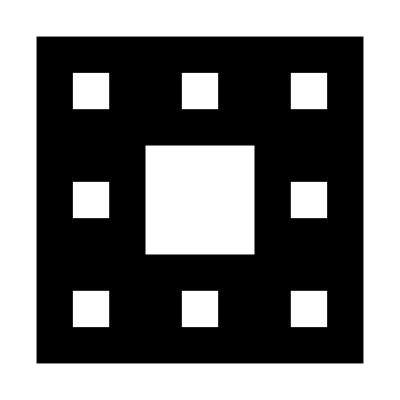
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawFrac[scarpet,Method->"Region"]
```

```mathematica
cdust={AffineTransform[{ScalingMatrix[{1/4,1/4}],{1/2,3/4}}],AffineTransform[{ScalingMatrix[{1/4,1/4}],{0,1/2}}],AffineTransform[{ScalingMatrix[{1/4,1/4}],{3/4,1/4}}],AffineTransform[{ScalingMatrix[{1/4,1/4}],{1/4,0}}]};
```

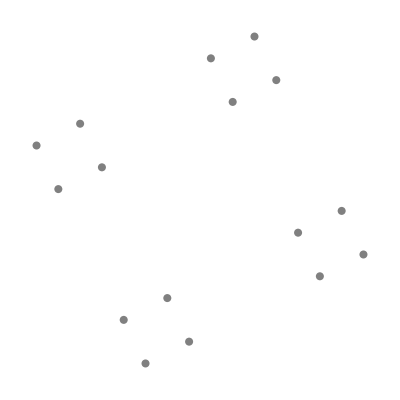
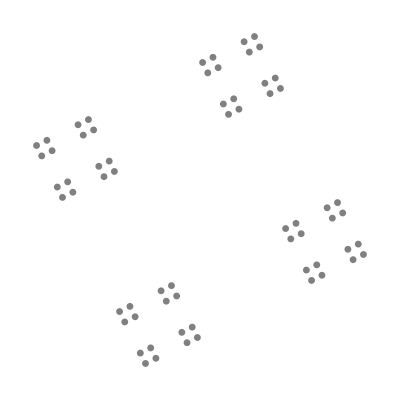
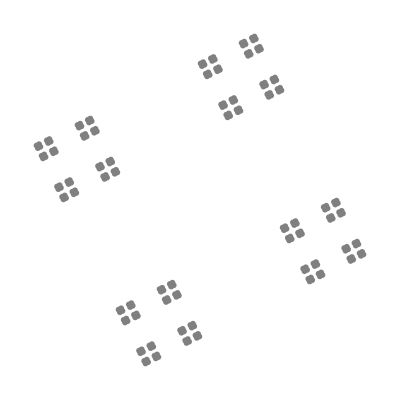
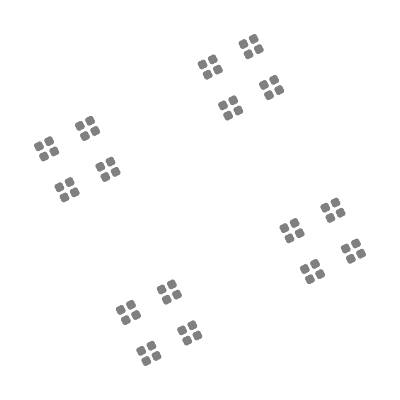
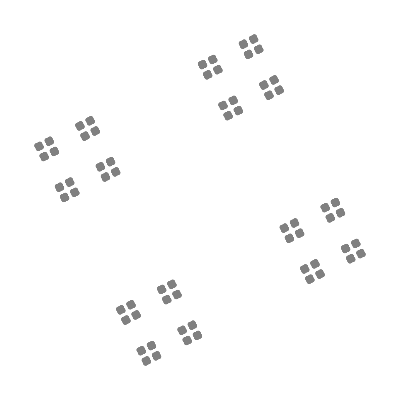
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawFrac[cdust]
```

```mathematica
msp={AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,0,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,1/3,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,2/3,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{1/3,0,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{1/3,2/3,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,0,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,1/3,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,2/3,0}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,0,1/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,0,1/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,2/3,1/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,2/3,1/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,0,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,1/3,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{0,2/3,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{1/3,0,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{1/3,2/3,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,0,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,1/3,2/3}}],AffineTransform[{ScalingMatrix[{1/3,1/3,1/3}],{2/3,2/3,2/3}}]};
```

```mathematica
DrawFrac[msp,"Approximation"->True]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
spyramid={SimTrans[1/2,{0,0,Sqrt[6]/3}],
SimTrans[1/2,{0,1/Sqrt[3],0}],
SimTrans[1/2,{1/2,-1/(2Sqrt[3]),0}],
SimTrans[1/2,{-1/2,-1/(2Sqrt[3]),0}]
};
```

Use Axes to control drawing axes

```mathematica
DrawFrac[spyramid,Method->"Lines",MaxIterations->4,Axes->True]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

## Possible problems

Dimension should be same

```mathematica
str={AffineTransform[{ScalingMatrix[{1/2}],{0}}],
AffineTransform[{ScalingMatrix[{1/2,1/2}],{Sqrt[3]/6,0}}],AffineTransform[{ScalingMatrix[{1/2,1/2}],{-Sqrt[3]/6,0}}]};
```

```mathematica
DrawFrac[str]
```

DrawFrac::wd: Dimension {1,2,2} should be same and less than 3

$Aborted

One will abort if use non-TransformationFunction and Region method.

```mathematica
ff[{x_,y_}]:={x/2+Sin[x],y/2+1/2};
ttf={ff,AffineTransform[{ScalingMatrix[{1/2,1/2}],{Sqrt[3]/6,0}}],AffineTransform[{ScalingMatrix[{1/2,1/2}],{-Sqrt[3]/6,0}}]};
DrawFrac[ttf,Method->"Region"]
```

DrawFrac::ch: Method ConvexHull does not apply to non affine transformation

$Aborted

This is because calculating the Region transformation for arbitrary functions can be very slow.

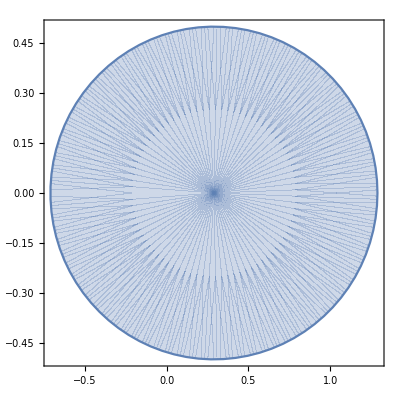
{0.022876,-Graphics-}

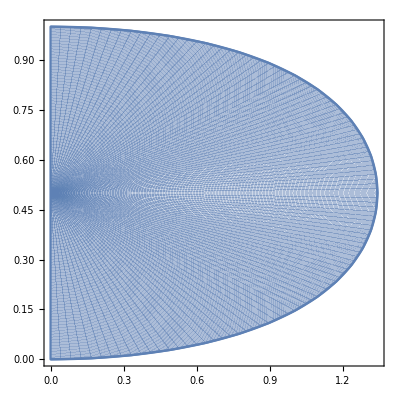
{6.69831,-Graphics-}

```mathematica
TransformedRegion[Disk[],AffineTransform[{ScalingMatrix[{1,1/2}],{Sqrt[3]/6,0}}]]//RegionPlot//Timing
TransformedRegion[Disk[],ff]//RegionPlot//Timing
(*注意下图绘制的不是圆*)
```

DrawFrac can also allow other transformation such as fractional linear transformation

{TransformationFunction[(1/2 | 0 | 0
0 | 1/2 | 1
0 | 1 | 1)],TransformationFunction[(1/2 | 0 | 1/(2 √3)
0 | 1/2 | 0
0 | 0 | 1)],TransformationFunction[(1/2 | 0 | -1/(2 √3)
0 | 1/2 | 0
0 | 0 | 1)]}

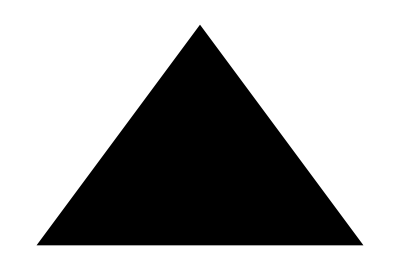
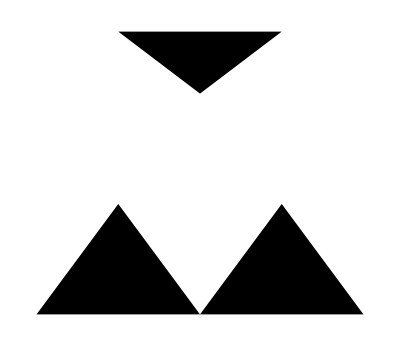
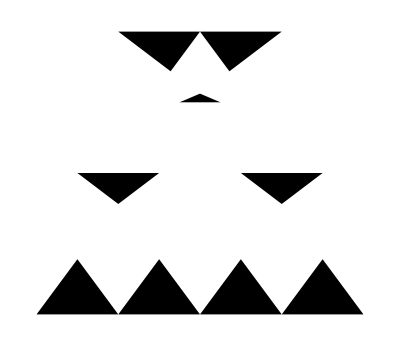
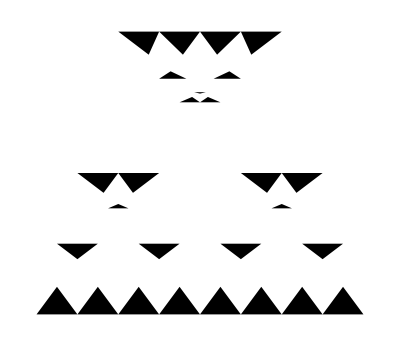
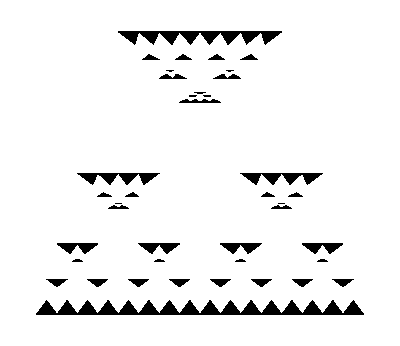

```mathematica
ttf={LinearFractionalTransform[{{{1/2,0},{0,1/2}}, {0,1},{0,1}}],AffineTransform[{ScalingMatrix[{1/2,1/2}],{Sqrt[3]/6,0}}],AffineTransform[{ScalingMatrix[{1/2,1/2}],{-Sqrt[3]/6,0}}]}
DrawFrac[ttf,Method->"Region",MaxIterations->4]
```

Sometimes the method Points and Region will be bad

```mathematica
astrig={SimTrans[((Sqrt[5]-1)/2)^2,{0,Sqrt[3]/2}],
SimTrans[((Sqrt[5]-1)/2),{-1/2,0}],
SimTrans[((Sqrt[5]-1)/2),{1/2,0}]
};
```

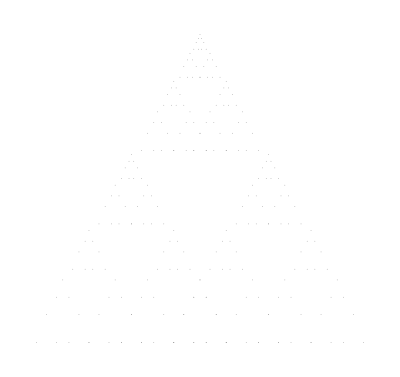
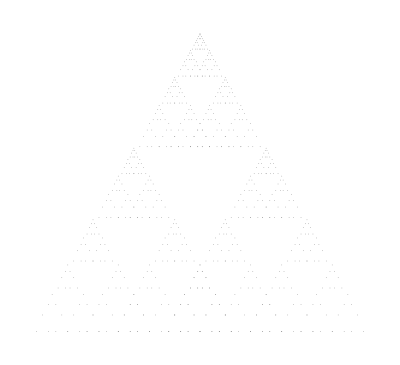
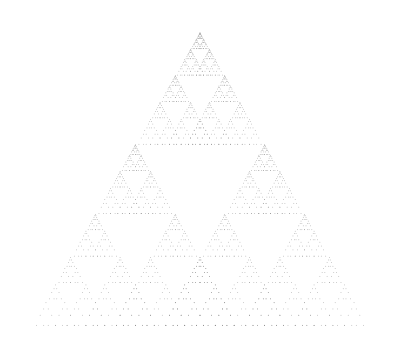
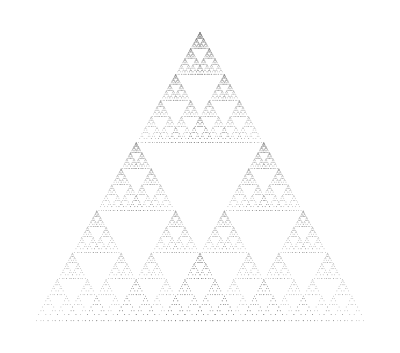
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
DrawFrac[astrig,"Size"->0.01]
```

Use Line method to this example.

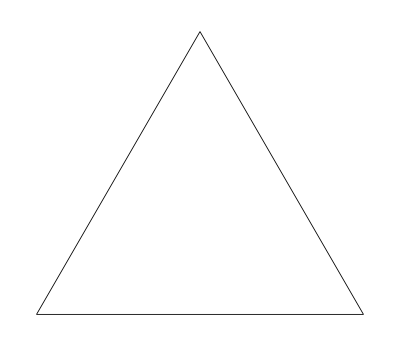
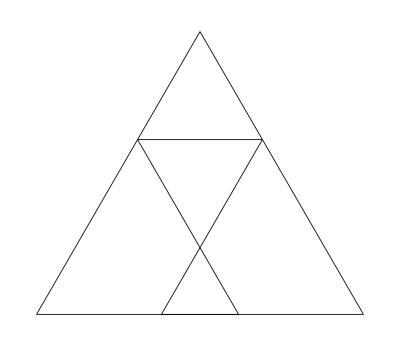
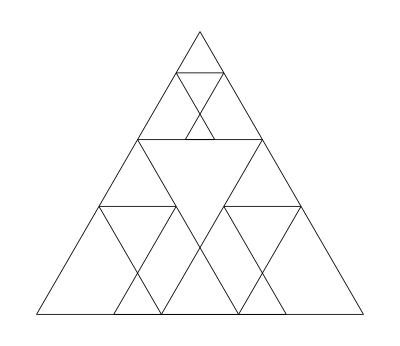
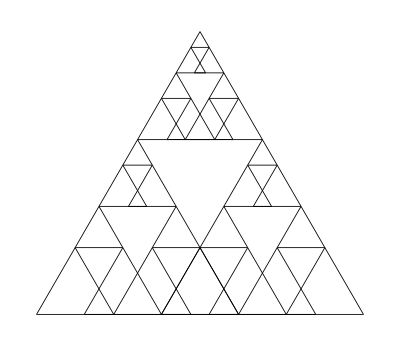

```mathematica
DrawFrac[astrig,Method->"Lines",MaxIterations->3]
```